```mathematica
s[t_]:=t^3-9/2 t^2-7t
s'[t]
s''[t]
Solve[s''[t]==0,t]
```

-7-9 t+3 t^2

-9+6 t

{{t→3/2}}

```mathematica
h[t_]:=10t-0.83 t^2;
Solve[h[t]==25,t]
h'[3.540297815892975]
```

{{t→3.5403},{t→8.50789}}

4.12311

```mathematica
h[t_]:=80t-16 t^2
h'[t]
Solve[h'[t]==0,t]//N
h[2.5]
```

80-32 t

{{t→2.5}}

100.

```mathematica
a[r_]:=π r^2
diff[r1_,r2_]:=(a[r2]-a[r1])/(r2-r1)//N
diff[2,2.1]
```

12.8805

```mathematica
Head[Pi//N]
```

Real

```mathematica
s[r_]:=4 π r^2;
s'[3]//N
```

75.3982

```mathematica
V[t_]:=5000(1-t/40)^2
V'[t]
V'[{5,10,20,40}]//N
```

250 (-1+t/40)

{-218.75,-187.5,-125.,0.}

```mathematica
250 (-1+t/40)//Simplify//N//Expand
```

-250.+6.25 t

```mathematica
F[r_]:=(G M m)/r^2
F'[r]
```

-(2 G m M)/r^3

```mathematica
Solve[-2==(-2k)/20000^3,k]
```

{{k→8000000000000}}

```mathematica
G'[r_]:=(-2 8 10^12)/r^3
G'[10000]
```

-16

```mathematica
n[t_]:=400 3^t
n'[t]
n'[2.5]
```

400 3^t Log[3]

6850.27

```mathematica
f[t_]:=140/(1+6 Exp[-0.7t])
f[t]
```

140/(1+6 ⅇ^(-0.7 t))

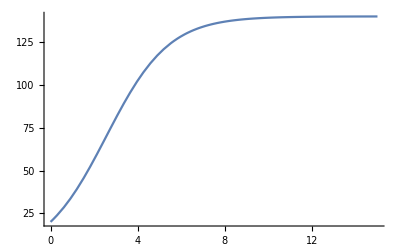

```mathematica
Plot[140/(1+6 ⅇ^(-0.7 t)),{t,0,15}]
```

```mathematica
Solve[{20==a/(1+b),12==(0.7a b)/(1+b)^2},{a,b}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→140.,b→6.}}

```mathematica
f[length_,tension_,density_]:=1/(2length)Sqrt[tension/density]
D[f[L,T,D],{T}]
```

1/(4 D L √(T/D))

```mathematica
cost[x_]:=1200+12x-0.1 x^2+0.0005 x^3
cost'[x]//TraditionalForm
cost'[200]
cost[201]-cost[200]
```

0.0015 x^2-0.2 x+12

32.

32.2005